# Primer examen de Métodos numéricos Nombre: Juan Manuel Gómez Portugal Zermeño A01372942

## Programas usados en el examen

```mathematica
bisec[f_, a1_, b1_,n_, pre_] := Module[{a=SetPrecision[a1, pre], b=SetPrecision[b1, pre]}, list = Table[c=(a+b)/2; If[(f/.x->c)(f/.x->b) < 0, N[a=c], N[b=c]], {n}]; 
error = Abs[list[[n]]-list[[n-1]]]/list[[n]];
{c, error}]
```

## 1- (6.15)

```mathematica
R = 0.518;
Pc = 4600;
Tc = 191;
T = 233.15;
p = 65;
a=0.427(R^2 Tc^2.5)/Pc;
b = 0.0866R(Tc/Pc);
f = Simplify[(R T)/(x - b)- a/(x(x+b)√T)-p]
NSolve[f, x, Reals]
v = 1.85307;
d = 3;
Print["El volumen de metano es: ", v, " m^3/kg"];
Print["La masa de metano es: ",  d/v, " kg"];
```

-0.822423/(x^2+0.00186262 x)+120.772/(x-0.00186262)-65

{{x→1.85307}}

El volumen de metano es: 1.85307 m^3/kg

La masa de metano es: 1.61894 kg

## 2 - (6.17)

{{x→1266.32}}

The value for TA is: 1266.32

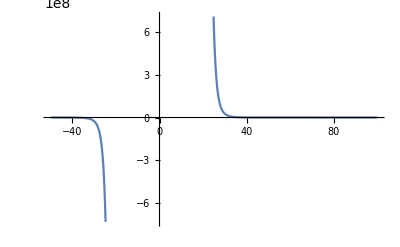

```mathematica
w = 10;
y0 = 5;
y17 = 15;
x17 = 50;
f17 =  x/w Cosh[w/x x17]+y0-x/w-y17;
NSolve[f17, x, Reals]
Ta = 1266.32;
Print["The value for TA is: ", Ta]
Print[Plot[f17, {x, -50, 100}]]
```

## 3 - (6.21)

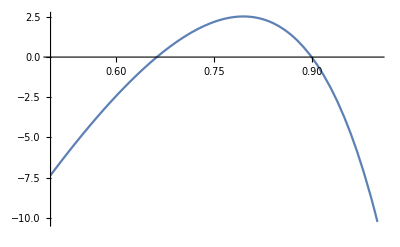

Se lanza a: 37.95898395° o 51.53174462°

```mathematica
v0 = 30;
df = 90;
h0 = 1.8;
hf = 1;
g = 9.81;
f21 = Tan[x]df-g/(2 v0^2(Cos[x])^2)df^2+h0 - hf;
Plot[f21, {x, 0.5, 1}]
r1 = (bisec[f21, 0.6, 0.7, 20, 10][[1]])(180/π);
r2 = bisec[f21, 0.8, 1, 20, 10][[1]](180/π);
Print["Se lanza a: ", r1 , "° o ", r2, "°"]
```

## 4 - (Newton-Raphson) Este programa calcula las raíces de una función haciendo uso de la aproximación de la derivada de la función. Sólo requiere una función, una aproximación de la raíz y el número de iteraciones. Use el programa para graficar el valor de la raíz vs. el error porcentual de la raíz. Usa la función-ejemplo que se da.

```mathematica
new[f_,a1_,n_]:=Module[{a=a1},
list = Table[b=a;{a=a-(f/.x->a)/(D[f,x]/.x->a),Abs[(b-a)/a 100]},{n}];
Print[list//MatrixForm];
ListPlot[list]]
```

(2.71377 | 121.095
1.61716 | 67.8107
1.12449 | 43.8126
0.925062 | 21.5586
0.879336 | 5.20009
0.876735 | 0.296706)

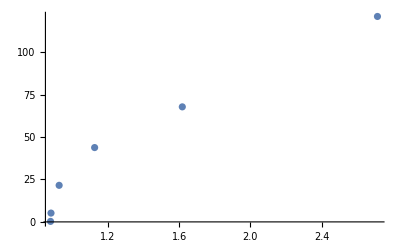

TraditionalForm

```mathematica
new[Sin[x]-x^2,6.,6]
$PrePrint=TraditionalForm
```

## 5 - (Programa) Hacer un programa que halle los máximos y mínimos y, los puntos silla de una función de dos variables. Corran la función-ejemplo. -Graphics-

```mathematica
f=x^3+y^3-3 x^2-3 y^2-9x;
```

```mathematica
disc[f_] := Module[{}, 
fx = D[f, {x}];
fxx = D[f, {x, 2}];
fy = D[f, {y}];
fyy = D[f, {y, 2}];
fxy = D[fx, {y}];
discr = (fxx)(fyy)-(fxy)^2;

]
```